```mathematica
path=NotebookDirectory[]<>"~images\\";
plotpath=NotebookDirectory[]<>"~plot\\";
datanames=("vorts"<>ToString[#]&)/@Join[Range[1,23],Range[25,99]];
xml=Import[path<>First@datanames<>".xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
```

```mathematica
pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
(*features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];*)
chartcolors=rgbcolors[[#]]&/@index;

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98
1 | 0.428693 | 0.411928 | 0.393121 | 0.373258 | 0.354988 | 0.354941 | 0.338802 | 0.326271 | 0.3139 | 0.331926 | 0.349342 | 0.359217 | 0.362728 | 0.364164 | 0.385295 | 0.403735 | 0.403768 | 0.413819 | 0.418209 | 0.415862 | 0.406058 | 0.392429 | 0.371329 | 0.404219 | 0.401792 | 0.383796 | 0.383769 | 0.365164 | 0.373052 | 0.384283 | 0.402225 | 0.413333 | 0.412608 | 0.403495 | 0.390967 | 0.372796 | 0.356815 | 0.356867 | 0.35227 | 0.35422 | 0.351002 | 0.346207 | 0.337446 | 0.322706 | 0.316359 | 0.316431 | 0.309613 | 0.292381 | 0.292415 | 0.295865 | 0.309949 | 0.324346 | 0.339015 | 0.351841 | 0.362688 | 0.366713 | 0.362217 | 0.347577 | 0.325953 | 0.325968 | 0.31358 | 0.301451 | 0.319679 | 0.345635 | 0.372949 | 0.396615 | 0.419573 | 0.435178 | 0.443432 | 0.449884 | 0.449788 | 0.450746 | 0.443108 | 0.432198 | 0.410034 | 0.378637 | 0.343069 | 0.306319 | 0.27186 | 0.28674 | 0.316594 | 0.316609 | 0.343992 | 0.368237 | 0.388583 | 0.401502 | 0.409358 | 0.406504 | 0.400341 | 0.383277 | 0.358273 | 0.325453 | 0.325438 | 0.290259 | 0.27578 | 0.287204 | 0.287196 | 0.277257
2 | 0.0911703 | 0.0912383 | 0.0917922 | 0.0937589 | 0.0951092 | 0.0950667 | 0.0951602 | 0.0945761 | 0.0942625 | 0.0930253 | 0.0928203 | 0.0934854 | 0.0942522 | 0.0958237 | 0.0972275 | 0.0974251 | 0.0974691 | 0.0971741 | 0.0974477 | 0.0978331 | 0.0990622 | 0.10056 | 0.103819 | 0.101291 | 0.101708 | 0.104571 | 0.104539 | 0.106546 | 0.105285 | 0.103912 | 0.101391 | 0.0998976 | 0.101035 | 0.100995 | 0.102048 | 0.103393 | 0.103624 | 0.103616 | 0.102771 | 0.101019 | 0.100182 | 0.100615 | 0.101702 | 0.104141 | 0.10533 | 0.106284 | 0.106685 | 0.106911 | 0.106931 | 0.10826 | 0.107864 | 0.107388 | 0.10617 | 0.105919 | 0.104981 | 0.104292 | 0.105218 | 0.107103 | 0.108384 | 0.108355 | 0.107833 | 0.107952 | 0.108197 | 0.10857 | 0.108117 | 0.106528 | 0.103268 | 0.099635 | 0.0961937 | 0.0935655 | 0.0935999 | 0.0919975 | 0.0931542 | 0.0950644 | 0.0995895 | 0.106853 | 0.113432 | 0.11738 | 0.118037 | 0.117886 | 0.115431 | 0.115445 | 0.111516 | 0.108959 | 0.105698 | 0.104502 | 0.102415 | 0.101152 | 0.100117 | 0.100165 | 0.101369 | 0.103782 | 0.103767 | 0.103936 | 0.104469 | 0.104733 | 0.106011 | 0.108356
3 | 0.0628405 | 0.0712886 | 0.0807399 | 0.0895763 | 0.0986244 | 0.0986717 | 0.109418 | 0.119716 | 0.130457 | 0.116847 | 0.103708 | 0.0967746 | 0.093956 | 0.0911766 | 0.0746203 | 0.0636139 | 0.0635253 | 0.0577716 | 0.0573262 | 0.0586427 | 0.0624924 | 0.0693326 | 0.0790134 | 0.0630929 | 0.0631919 | 0.0690356 | 0.0689757 | 0.0761595 | 0.0720545 | 0.0659948 | 0.0593455 | 0.0537352 | 0.0524954 | 0.0564111 | 0.0629654 | 0.0731205 | 0.0818984 | 0.0818798 | 0.0865083 | 0.0870983 | 0.0902526 | 0.0938756 | 0.0984849 | 0.105166 | 0.106661 | 0.104983 | 0.107915 | 0.118689 | 0.118648 | 0.114255 | 0.103603 | 0.0950316 | 0.0870776 | 0.0811762 | 0.0756333 | 0.075526 | 0.0786879 | 0.0854321 | 0.0962958 | 0.0962563 | 0.104051 | 0.111462 | 0.0983604 | 0.0826294 | 0.0672464 | 0.0547001 | 0.0464982 | 0.0436045 | 0.0429586 | 0.0422013 | 0.0421788 | 0.0433287 | 0.0461225 | 0.0487503 | 0.0544324 | 0.0639929 | 0.075675 | 0.0908108 | 0.110448 | 0.100366 | 0.0864476 | 0.0864477 | 0.0746139 | 0.0666541 | 0.0611248 | 0.0566686 | 0.05488 | 0.0586795 | 0.0630185 | 0.0711981 | 0.0846401 | 0.101788 | 0.101792 | 0.124506 | 0.134281 | 0.122598 | 0.119094 | 0.122214

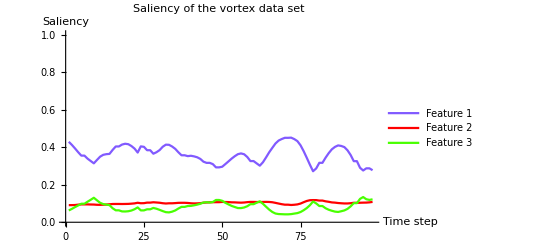

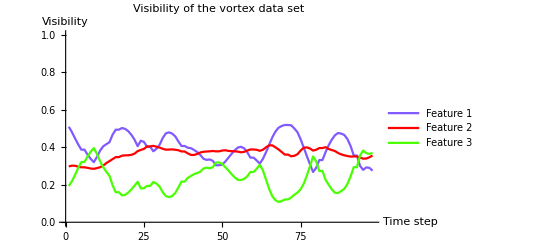

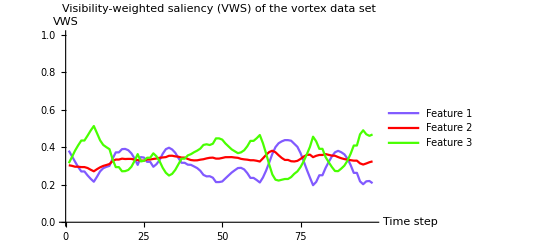

```mathematica
resultxml="D:\\document\\work\\time-varying-visualization\\~images\\saliency.xml";
scoremap=If[FileExistsQ[resultxml],Association@Import[resultxml],<||>];
features=Table[scoremap[#][[1]][[i]]&/@datanames,{i,Range[3]}];
TableForm[features,TableHeadings->Automatic]
ListLinePlot[features,PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Saliency of the vortex data set",AxesLabel->{"Time step","Saliency"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors]
ListLinePlot[Table[scoremap[#][[2]][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Visibility of the vortex data set",AxesLabel->{"Time step","Visibility"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors]
ListLinePlot[Table[scoremap[#][[5]][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Visibility-weighted saliency (VWS) of the vortex data set",AxesLabel->{"Time step","VWS"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors]
```

```mathematica
recordxml="D:\\document\\work\\time-varying-visualization\\~plot\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
parallinesearch=recordmap[First@datanames][[4]][[3]]
```

{0.,0.0406269,1.}

```mathematica
tfinames=(plotpath<>#<>"_optimized_parallelsearch.tfi"&)/@datanames
```

{D:\document\work\time-varying-visualization\~plot\vorts1_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts2_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts3_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts4_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts5_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts6_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts7_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts8_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts9_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts10_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts11_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts12_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts13_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts14_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts15_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts16_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts17_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts18_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts19_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts20_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts21_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts22_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts23_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts25_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts26_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts27_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts28_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts29_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts30_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts31_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts32_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts33_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts34_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts35_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts36_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts37_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts38_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts39_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts40_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts41_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts42_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts43_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts44_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts45_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts46_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts47_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts48_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts49_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts50_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts51_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts52_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts53_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts54_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts55_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts56_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts57_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts58_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts59_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts60_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts61_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts62_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts63_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts64_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts65_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts66_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts67_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts68_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts69_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts70_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts71_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts72_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts73_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts74_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts75_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts76_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts77_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts78_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts79_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts80_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts81_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts82_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts83_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts84_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts85_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts86_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts87_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts88_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts89_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts90_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts91_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts92_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts93_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts94_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts95_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts96_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts97_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts98_optimized_parallelsearch.tfi,D:\document\work\time-varying-visualization\~plot\vorts99_optimized_parallelsearch.tfi}